```mathematica
AppendTo[$Path,ParentDirectory@NotebookDirectory[]];
Needs["AstronomicalDiaries`"]
```

```mathematica
$ADBase=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Data"}];
```

```mathematica
observations=ADObservations[];
```

```mathematica
textid="X201941";
```

```mathematica
Dataset@Select[observations,#TextID===textid&][[All,{"Line","EarliestDay","LatestDay","Object","Relation","Cubits","Fingers","Reference"}]]
```

```mathematica
Dataset@Select[modelObservations,#TextID===textid&][[All,{"Line","EarliestDay","LatestDay","Object","Relation","Cubits","Fingers","Reference"}]]
```

```mathematica
Position[modelObservations[[All,"TextID"]],textid][[All,1]]
```

{1304,1305,1306,1307,1308,1309}

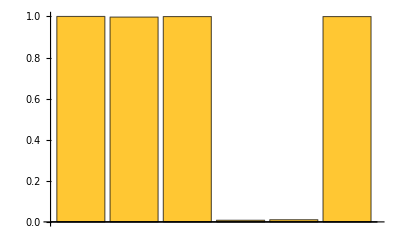
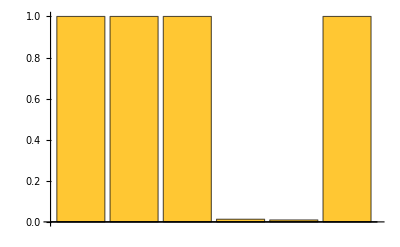
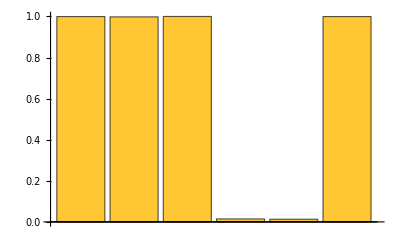
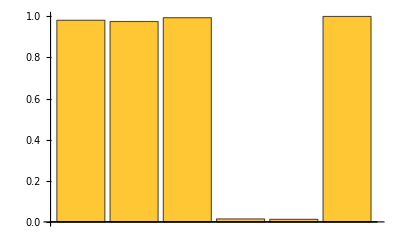

```mathematica
BarChart/@N[Mean/@chains[[All,All,"m",{1304,1305,1306,1307,1308,1309}]]]
```

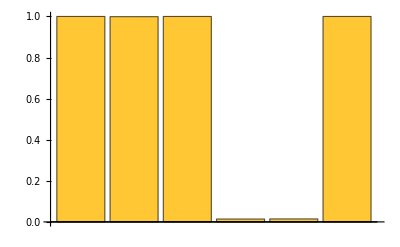
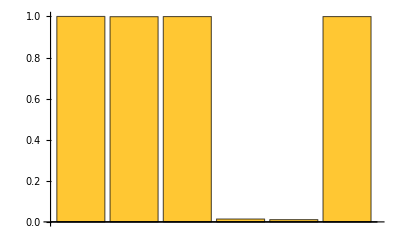
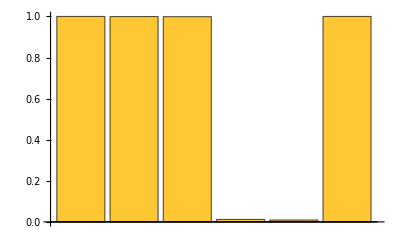
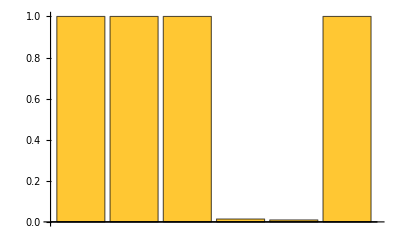

```mathematica
BarChart/@N[Mean/@chainsYears[[All,All,"m",{1304,1305,1306,1307,1308,1309}]]]
```

```mathematica
setObsSEYear[obs_,seYear_]:=
<|
obs,
"SEYear"->seYear,
"Date"->ADFromBabylonianDate[{seYear,obs["Month"],obs["Day"]}]
|>
```

```mathematica
Select[observations,#TextID===textid&][[3]]
```

<|ID→{X201941,{890,932}},Object→Moon,Relation→Behind,Reference→Spica,Cubits→3/2,Fingers→Missing[],Time→BeginningOfTheNight,Day→7,EarliestDay→7,LatestDay→7,Month→III,RegnalYear→{SE,117},SEYear→117,Date→Tue 13 Jun 195 BCJulian,EarliestDate→Tue 13 Jun 195 BCJulian,LatestDate→Tue 13 Jun 195 BCJulian,Damaged→False,Line→o 8',TextID→X201941,Range→{890,932},TimeRange→{866,887},EarliestDayRange→{848,861},LatestDayRange→{848,861}|>

```mathematica
ADObservationPlot[Select[observations,#TextID===textid&][[3]],"HideEarth"->True]
```

the moon was 1 1/2 cubits behind α Virginis

-Graphics-

```mathematica
ADObservationPlot[setObsSEYear[Select[observations,#TextID===textid&][[4]],187],"HideEarth"->False,AstroRange->Quantity[20, "AngularDegrees"]]
```

the moon was 1 cubit behind β Librae

-Graphics-

```mathematica
d=DateObject[Today,"Instant"]
```

Tue 16 Sep 2025 00:00:00

```mathematica
AstroPosition[Entity["Planet","Jupiter"],{"Horizon","Date"->{d,d+Quantity[1,"Minutes"],d+Quantity[2,"Minutes"]},"Location"->GeoPosition[{32.5425,44.421111}]}]
```

AstroPosition::date: Cannot interpret date GeoPosition[{32.5425,44.4211}].

AstroPosition[Jupiter,{Horizon,Date→{Tue 16 Sep 2025 00:00:00,Tue 16 Sep 2025 00:01:00,Tue 16 Sep 2025 00:02:00},Location→GeoPosition[{32.5425,44.4211}]}]